# 1. vaja: Osnove Mathematice

1. S pomočjo mathematice izračunaj.

```mathematica
(1/3 + 1/6)^2
```

1/4

```mathematica
3/(6/8)
```

4

```mathematica
Sin[Pi/2]
```

1

```mathematica
Exp[Log[7]]
```

7

2. Poenostavi naslednje izraze.

```mathematica
Factor[((3+4x)/(2+5x))^2 + ((2+x)/(1-x))^2]
```

(25+102 x+161 x^2+112 x^3+41 x^4)/((-1+x)^2 (2+5 x)^2)

```mathematica
Factor[x/y+y/x+2]
```

(x+y)^2/(x y)

```mathematica
Factor[(x^2+ y^2)^2 -2(x*y)^2]
```

x^4+y^4

```mathematica
Simplify[Sin[x]^2+Cos[x]^2]
```

1

```mathematica
FullSimplify[Tan[Pi/8]^4 + Cot[Pi/8]^4]
```

34

```mathematica
FullSimplify[Sqrt[278+42*Sqrt[5]-12*Sqrt[6]-28*Sqrt[30]]]
```

3+7 √5-2 √6

3.  Razstavi izraz (x + xy + y)^10. Razstavi še izraz sin(x + y). (Nasvet: TrigExpand)

```mathematica
Expand[(x+x*y+y)^10]
```

x^10+10 x^9 y+10 x^10 y+45 x^8 y^2+90 x^9 y^2+45 x^10 y^2+120 x^7 y^3+360 x^8 y^3+360 x^9 y^3+120 x^10 y^3+210 x^6 y^4+840 x^7 y^4+1260 x^8 y^4+840 x^9 y^4+210 x^10 y^4+252 x^5 y^5+1260 x^6 y^5+2520 x^7 y^5+2520 x^8 y^5+1260 x^9 y^5+252 x^10 y^5+210 x^4 y^6+1260 x^5 y^6+3150 x^6 y^6+4200 x^7 y^6+3150 x^8 y^6+1260 x^9 y^6+210 x^10 y^6+120 x^3 y^7+840 x^4 y^7+2520 x^5 y^7+4200 x^6 y^7+4200 x^7 y^7+2520 x^8 y^7+840 x^9 y^7+120 x^10 y^7+45 x^2 y^8+360 x^3 y^8+1260 x^4 y^8+2520 x^5 y^8+3150 x^6 y^8+2520 x^7 y^8+1260 x^8 y^8+360 x^9 y^8+45 x^10 y^8+10 x y^9+90 x^2 y^9+360 x^3 y^9+840 x^4 y^9+1260 x^5 y^9+1260 x^6 y^9+840 x^7 y^9+360 x^8 y^9+90 x^9 y^9+10 x^10 y^9+y^10+10 x y^10+45 x^2 y^10+120 x^3 y^10+210 x^4 y^10+252 x^5 y^10+210 x^6 y^10+120 x^7 y^10+45 x^8 y^10+10 x^9 y^10+x^10 y^10

```mathematica
TrigExpand[Sin[x+y]]
```

Cos[y] Sin[x]+Cos[x] Sin[y]

4. Naj bo a = 3, b = 4 in c = 6. Definiraj spremenljivki o = a + b + c in s = o 2. Koliko znaša sqrt(s(s−a)(s−b)(s−c))? Kateri geometrijski pomen ima to število? Uporabljene spremenljivke a,b,c,o,s na koncu izbriši.

```mathematica
a = 3
b = 4
c = 6
```

3

4

6

```mathematica
o = a +b + c
```

13

```mathematica
s = o/2
```

13/2

```mathematica
Sqrt[s(s-a)(s-a)(s-a)]
```

(7 √91)/4

To število je ploščina trikotnika s stranicmi dolžine 3,4 in 6. Imenuje se Heronov obrazec.

```mathematica
Clear[a]
Clear[b]
Clear[c]
Clear[o]
Clear[s]
```

5. V Mathematici defniraj seznam s = {3,2,0,0,5,13,2,−x,8}. Z uporabo ukaza s[[5]] poišči 5. element tega seznama. Kaj pa vrne ukaz s[[-1]]?

```mathematica
s = {3,2,0,0,5,13,2,-x,8}
```

{3,2,0,0,5,13,2,-x,8}

```mathematica
s[[5]]
```

5

```mathematica
s[[-1]]
```

8

Ukaz vrne zadnji element v množici.

6. Nariši graf funkcije sin(2x + π 4)− 1 2 na intervalu [−2π,2π].

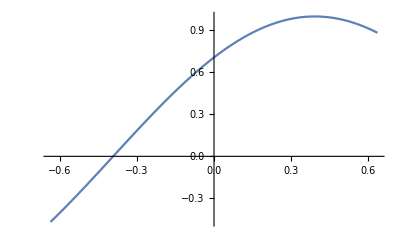

```mathematica
Plot[Sin[2x +Pi/4],{x,-2/Pi,2/Pi}]
```

7. Definiraj funkciji f(x) = 5sin(x−2) in g(x) = 2^x −6 in ju vriši v isti koordinatni sistem. Interval izberi tako, da bodo na sliki vidna vsa presečišča obeh grafov.

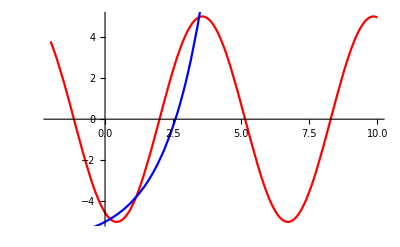

```mathematica
Show[{
Plot[5*Sin[x-2],{x,-2,10},PlotStyle->Red],
Plot[2^x-6,{x,-2,10},PlotStyle->Blue]
}]
```

8. Definiraj števili a = 3^200 +20 in b = 2^300 +30. V Mathematici preveri, ali velja a = b, a < b, ali pa morda a > b.

```mathematica
a = 3^200 + 20
b = 2^300 + 30
```

265613988875874769338781322035779626829233452653394495974574961739092490901302182994384699044021

2037035976334486086268445688409378161051468393665936250636140449354381299763336706183397406

```mathematica
a == b
```

False

```mathematica
a < b
```

False

```mathematica
a > b
```

True

9. Poišči vse rešitve enačbe x^2 + 4x + 2 = 0 z uporabo ukaza Solve. Kaj pa so rešitve enačbe x^2 + 4x + 5 = 0?

```mathematica
Solve[x^2 +4x + 2 == 0]
```

{{x→-2-√2},{x→-2+√2}}

```mathematica
Solve[x^2 +4x+5 == 0]
```

{{x→-2-ⅈ},{x→-2+ⅈ}}

Rešitvi druge enačbe sta kompleksni, in sicer x = -2 ± i

10. Poišči rešitve enačbe x^4 = 1 z uporabo ukaza Reduce.

```mathematica
Reduce[x^4 == 1]
```

x==-1||x==-ⅈ||x==ⅈ||x==1

11. (a) Definiraj funkcijo f(x) = (x^2 − 3rt(x^2))e^x. 
       (b) Nariši graf funkcije f na intervalu [−4,2]. Ali lahko iz grafa razbereš ničle funkcije f? Katere so? 
       (c) Zdaj poišči ničle funkcije f najprej s pomočjo ukaza Solve in nato Reduce. Kaj opaziš?

```mathematica
f[x_] := (x^2 - CubeRoot[x^2])*Exp[x]
```

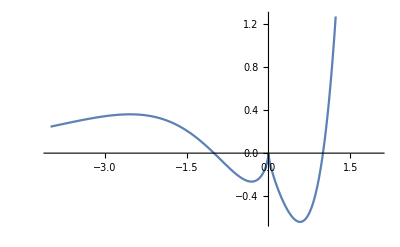

```mathematica
Plot[f[x],{x,-4,2}]
```

Da, iz grafa lahko razberem ničle x = ±1 in x = 0.

```mathematica
Solve[f[x] == 0,x]
```

{{x→-1},{x→0},{x→1}}

```mathematica
Reduce[f[x] == 0,x]
```

x==-1||x==0||x==1

Rešitve dobim v različnih oblikah.